## Calculations for g-factors of the ground state which take into account mixing between J levels within hyperfine states of the same F._□

```mathematica
(*Below I have written down the effective Hamiltonian for the ground state for a given N so that it is labelled M'N'. M just stands for 'matrix'. Eigenvalues give energy shift relative to N. Details on how to calculate the matrix elements are found in mathematica nb: BaH_GroundState_diagonalization.nb.

The approach here is to find H_gnd+H_zeeman and diagonalize together.*)
```

```mathematica
b=10;(*47 or 97 for SrF*)
γ=5762.;(*5700 or 75 for SrF*)
c1=10(*30 for SrF*);
μB=1.39996;(*MHz/Gauss*)
```

```mathematica
M1={{γ/2+b/4+c1/20,,0,0},{0,γ/2-b (5/12)-c1/(12),(b √2)/3+c1*Sqrt[2]/6,0},{0,(b √2)/3+c1*Sqrt[2]/6,-γ-b/12+c1/12,0},{0,0,0,-γ+b/4-c1/4}}; 
M1e=Eigenvalues[M1];(*This is the one we care about*)
{M1e[[1]]-M1e[[2]],M1e[[3]]-M1e[[4]]}
```

{-0.00578837,7.99421}

```mathematica
{M1e[[1]]-M1e[[2]],M1e[[3]]-M1e[[4]]}
```

{-8643.-(3 c2)/10,1/2 (-2906.-0.5 √(2.97663×10^8-11324. c2+1. c2^2))+1/2 (2906.-0.5 √(2.97663×10^8-11324. c2+1. c2^2))}

```mathematica
{-5765.973565552155,-5750.25,2892.75,2861.473565552155}
```

{-5765.97,-5750.25,2892.75,2861.47}

```mathematica
M0={{b/4+c1/12,0,0,0},{0,-b (3/4),0,0},{0,0,-γ/2+b /4,0},{0,0,0,-γ/2+b/4}};
M0e=Eigenvalues[M0]//N
{M0e[[1]]-M0e[[2]],M0e[[3]]-M0e[[4]]}
```

{-2867.75,-2867.75,-39.75,16.8333}

{0.,-56.5833}

```mathematica
M2={{γ+b/4,0,0,0},{0,γ-b (7./20),b√6/20,0},{0,b√6/20,-3γ/2-b (3/20),0},{0,0,0,-3γ/2+b/4}};
Eigenvalues[M2]
```

{-8650.05,-8631.25,5773.75,5745.55}

```mathematica
Eigenvectors[M2]
```

{{0.,-0.000399865,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.000399865,0.}}

```mathematica
Eigenvectors[M1]
```

{{0.,-0.00256809,0.999997,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.999997,0.00256809,0.}}

```mathematica
(*g factor calculator using the semi-classical g-factor approach - neglects mixing between j states*)
S=1/2;
F=1;
J1=3/2;
J2=1/2;
n=1.;
g1=2((S(S+1)-n(n+1)+J1(J1+1))/(2J1(J1+1)))(F(F+1)-S(S+1)+J1(J1+1))/(2F(F+1))
g2=2((S(S+1)-n(n+1)+J2(J2+1))/(2J2(J2+1)))(F(F+1)-S(S+1)+J2(J2+1))/(2F(F+1))
g1*.79+g2*.21 (*???*)
```

0.833333

-0.333333

0.588333

```mathematica
(*calculator for Zeeman hamiltonian components for hunds case B only. Change J, Jprime, F and mf values to get matrix elements. Hzx is the sum of eqs 8.183 and 8.185 in B&C -> the spin and nuclear zeeman terms added together.Needs to be multiplied by μ_B. For Lambda =/= 0,+1*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(Fp+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,J,S},{Jp,Fp,1}](-1)^(Jp+n+1+S)Sqrt[(2Jp+1)(2J+1)]*SixJSymbol[{J,n,S},{np,Jp,1}]*(-1)^(n-Λ)ThreeJSymbol[{n,-Λ},{1,0},{np,Λ}]Sqrt[(2np+1)(2n+1)]*Λ*)
S=1/2;
J=3/2.;
Jp=1/2;
F=2;
Fp=1;
mf=-1;
n=1;
np=1.;
Λ=0;
Hzx=2*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(Fp+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,J,S},{Jp,Fp,1}](-1)^(J+n+1+S)Sqrt[(2Jp+1)(2J+1)]*SixJSymbol[{J,S,n},{S,Jp,1}]Sqrt[S(S+1)(2S+1)]+-(5.585/1836)*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(F+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,S,J},{S,Fp,1}]Sqrt[S(S+1)(2S+1)]
```

-0.815179+7.99936×10^-16 ⅈ

Using the calculator above, I find all the non zero matrix elements for the complete Zeeman hamiltonian for all the ground state hyperfine sublevels.

```mathematica
Hz=ConstantArray[0,{4,4}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
BΣ=({{-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 50}});
```

```mathematica
HzBΣ=({{0.998479, 0, 0, 0}, {0, 0, 0, 1.00152}, {0, 0, -0.998479, 0}, {0, 1.00152, 0, 0}});
Eigensystem[HzBΣ];
Bsigfields=13*{2,4,6,-6,-4,-2}-0;
BSigsplittings=2*Abs[{56.8,93.7,132.2,-150.69,-104,-47.65}];
BSigsplittingsErrs={ErrorBar[5,4.5],ErrorBar[5,7.2],ErrorBar[5,5.6],ErrorBar[5,5.5],ErrorBar[5,9.8],ErrorBar[5,10.4]};
Export["BSigmaZeeman-data.png",Show[ErrorListPlot[Transpose[{Transpose[{Bsigfields,BSigsplittings}],BSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{(Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*1.1,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*0.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{Automatic}],Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic],ImageResolution->500]
```

BSigmaZeeman-data.png

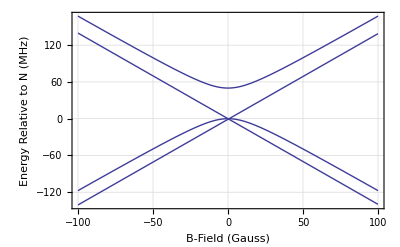

```mathematica
Plot[Eigenvalues[BΣ+μB*bz*HzBΣ],{bz,-100,100},PlotRange->{Automatic},Frame->True,FrameLabel->{"B-Field (Gauss)","Energy Relative to N (MHz)"},LabelStyle->Directive[Medium],GridLines->Automatic]
```

```mathematica
Hz=({{0.998479, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0.49924, 0, 0, 0, 0.289992, 0, 0, -0.815179, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0.334854, 0, 0, -0.941288, 0, 0}, {0, 0, 0, -0.49924, 0, 0, 0, 0.289992, 0, 0, 0.815179, 0}, {0, 0, 0, 0, -0.998479, 0, 0, 0, 0, 0, 0, 0}, {0, 0.289992, 0, 0, 0, 0.834094, 0, 0, 0.472165, 0, 0, -0.942809}, {0, 0, 0.334854, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0.289992, 0, 0, 0, -0.834094, 0, 0, -0.472165, 0}, {0, -0.815179, 0, 0, 0, 0.472165, 0, 0, -0.334854, 0, 0, 0}, {0, 0, -0.941288, 0, 0, 0, 0, 0, 0, 0, 0, -0.331812}, {0, 0, 0, 0.815179, 0, 0, 0, -0.472165, 0, 0, 0.334854, 0}, {0, 0, 0, 0, 0, -0.942809, 0, 0, 0, -0.331812, 0, 0}});
Transpose[Hz]==Hz
Eigenvalues[Hz]
```

True

{1.57111,-1.42836,-1.16346,-0.999758,0.999245,0.998479,-0.998479,0.997821,0.873564,-0.443683,-0.422513,0.0160366}

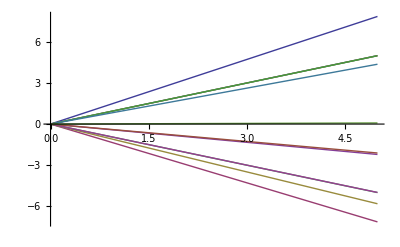

```mathematica
Plot[{bz*1.571110686186622,bz*-1.4283609479493216,bz*-1.163462946738257,bz*-0.9997575953964061,bz*0.9992453071623061,bz*-0.998479,bz*0.998479,bz*0.9978205194373678,bz*0.8735642915216771,bz*-0.44368334357235534,bz*-0.4225125963638776,bz*0.016036625712244856},{bz,0,5}]
```

```mathematica
MZ={{0.49924,0,0,0},{0,0.834094,0.469884,0},{0,0.46988,-0.334854,0},{0,0,0,0}};
MatrixForm[MZ]
Eigenvalues[MZ]
```

(0.49924 | 0 | 0 | 0
0 | 0.834094 | 0.469884 | 0
0 | 0.46988 | -0.334854 | 0
0 | 0 | 0 | 0)

{0.999553,-0.500313,0.49924,0.}

```mathematica
MT=M1+Bz *MZ//N
Eigenvalues[MT]
```

{{2892.75+0.49924 Bz,0.,0.,0.},{0.,2861.42+0.834094 Bz,22.156+0.469884 Bz,0.},{0.,22.156+0.46988 Bz,-5765.92-0.334854 Bz,0.},{0.,0.,0.,-5750.25}}

{-5750.25,2892.75+0.49924 Bz,1/2 (-2904.5+0.49924 Bz-1.49987 √(3.30872×10^7+9002.99 Bz+1. Bz^2)),1/2 (-2904.5+0.49924 Bz+1.49987 √(3.30872×10^7+9002.99 Bz+1. Bz^2))}

```mathematica
Eigenvalues[MT]-Eigenvalues[M1](*g factors accounting for J mixing*)
```

{15.7236,8643.+0.49924 Bz,-2892.75+1/2 (-2904.5+0.49924 Bz-1.49987 √(3.30872×10^7+9002.99 Bz+1. Bz^2)),-2861.47+1/2 (-2904.5+0.49924 Bz+1.49987 √(3.30872×10^7+9002.99 Bz+1. Bz^2))}

Here is the effective hamiltonian including spin rotation, and spin spin

```mathematica
Hfull=({{2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0}, {0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -5750.25}});
```

Made change to above matrix on 2/8 because was not properly symmetric due to input typo. Did not change anything too significantly...

```mathematica
Hall=Hfull+μB*(64.5)*Hz;
Hall//MatrixForm
mean=((Eigenvalues[Hall][[4]]+Eigenvalues[Hall][[3]])/2+(Eigenvalues[Hall][[2]]+Eigenvalues[Hall][[1]])/2)/2
mean-(Eigenvalues[Hall][[4]]+Eigenvalues[Hall][[3]])/2
mean-(Eigenvalues[Hall][[2]]+Eigenvalues[Hall][[1]])/2
```

(2982.91 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2937.83 | 0 | 0 | 0 | 26.1855 | 0 | 0 | -73.6086 | 0 | 0 | 0
0 | 0 | 2892.75 | 0 | 0 | 0 | 30.2365 | 0 | 0 | -84.9959 | 0 | 0
0 | 0 | 0 | 2847.67 | 0 | 0 | 0 | 26.1855 | 0 | 0 | 73.6086 | 0
0 | 0 | 0 | 0 | 2802.59 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.1855 | 0 | 0 | 0 | 2936.73 | 0 | 0 | 64.7913 | 0 | 0 | -85.1332
0 | 0 | 30.2365 | 0 | 0 | 0 | 2861.42 | 0 | 0 | 22.156 | 0 | 0
0 | 0 | 0 | 26.1855 | 0 | 0 | 0 | 2786.1 | 0 | 0 | -20.4793 | 0
0 | -73.6086 | 0 | 0 | 0 | 64.7913 | 0 | 0 | -5796.16 | 0 | 0 | 0
0 | 0 | -84.9959 | 0 | 0 | 0 | 22.156 | 0 | 0 | -5765.92 | 0 | -29.9618
0 | 0 | 0 | 73.6086 | 0 | 0 | 0 | -20.4793 | 0 | 0 | -5735.68 | 0
0 | 0 | 0 | 0 | 0 | -85.1332 | 0 | 0 | 0 | -29.9618 | 0 | -5750.25)

-5762.88

-30.7126

30.7126

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Eigenvalues[Hfull+μB*80*Hz]
Xsigfields=13*{5.026,6,7.035,4.072,-5.02,-4.025,-6.01,-7};
XSigsplittings=2*Abs[{34.79,38.15,43.28,24.66,-33.65,-22.65,-42.05,-48.72}];
XSigsplittingsErrs={ErrorBar[10.4],ErrorBar[6.9],ErrorBar[4.9],ErrorBar[3.2],ErrorBar[8.7],ErrorBar[5.6],ErrorBar[6.3],ErrorBar[4.8]};
Export["XSigmaZeeman.jpeg",Show[ErrorListPlot[Transpose[{Transpose[{Xsigfields,XSigsplittings}],XSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2,(-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2)*1.1,(-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2)*.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{Automatic}],Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic],ImageResolution->500]
```

{-5805.07,-5797.33,-5729.5,-5721.41,3004.58,2985.08,2921.3,2918.39,2850.37,2837.12,2780.92,2755.55}

XSigmaZeeman.jpeg

```mathematica
Transpose[{Transpose[{Xsigfields,XSigsplittings}],XSigsplittingsErrs}]
Epig=-0.0328126;
```

{{{63.2271,69.58},ErrorBar[10.4]},{{75.48,76.3},ErrorBar[6.9]},{{88.5003,86.56},ErrorBar[4.9]},{{51.2258,49.32},ErrorBar[3.2]},{{-63.1516,67.3},ErrorBar[8.7]},{{-50.6345,45.3},ErrorBar[5.6]},{{-75.6058,84.1},ErrorBar[6.3]},{{-88.06,97.44},ErrorBar[4.8]}}

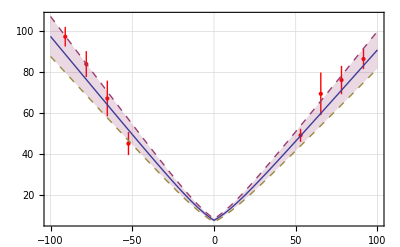

```mathematica
Show[ErrorListPlot[Transpose[{Transpose[{Xsigfields,XSigsplittings}],XSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2+Epig*bz,(-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2+Epig*bz)*1.1,(-(Eigenvalues[Hfull+μB*bz*Hz][[1]]+Eigenvalues[Hfull+μB*bz*Hz][[2]])/2+(Eigenvalues[Hfull+μB*bz*Hz][[3]]+Eigenvalues[Hfull+μB*bz*Hz][[4]])/2+Epig*bz)*.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{Automatic}],Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic]
```

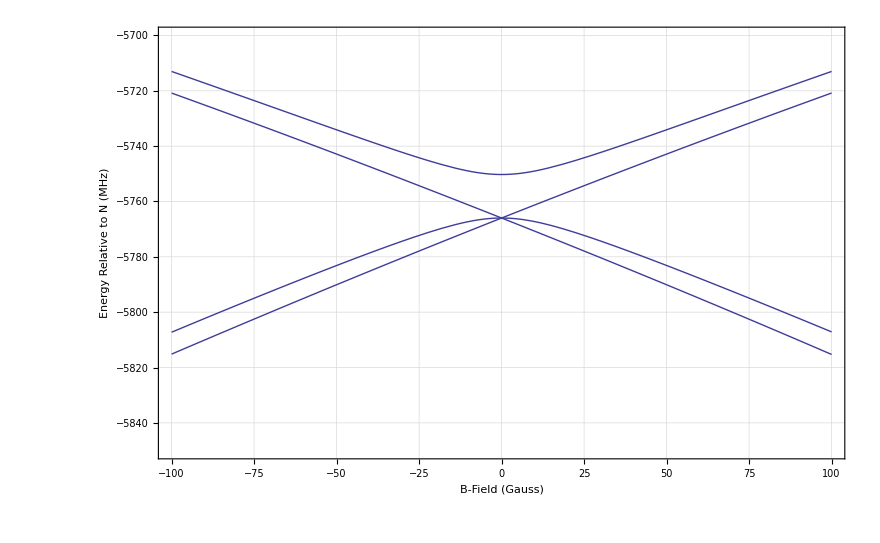

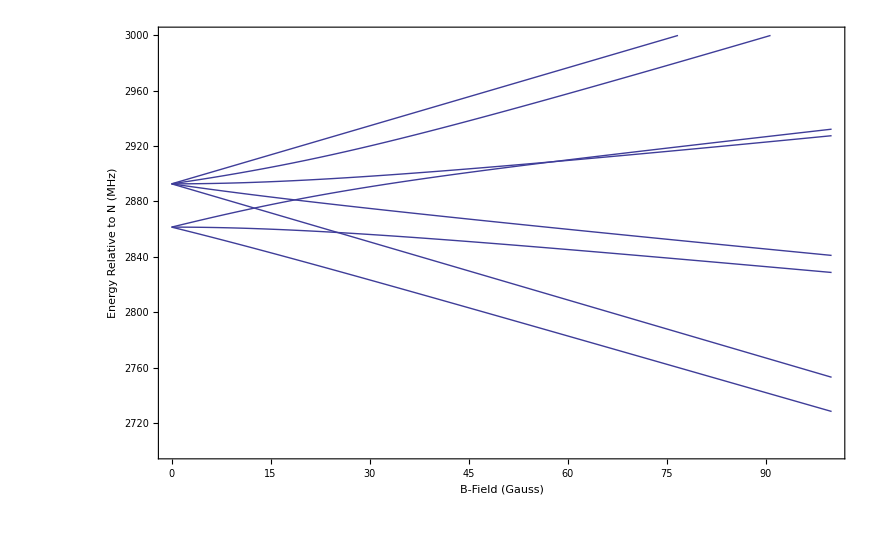

```mathematica
Plot[{Eigenvalues[Hfull+μB*bz*Hz],Eigenvalues[BΣ+μB*bz*HzBΣ]},{bz,-100,100},PlotRange->{-5850,-5700},Frame->True,FrameLabel->{"B-Field (Gauss)","Energy Relative to N (MHz)"},LabelStyle->Directive[Medium],GridLines->Automatic]
Plot[Eigenvalues[Hfull+μB*bz*Hz],{bz,0,100},PlotRange->{2700,3000},Frame->True,FrameLabel->{"B-Field (Gauss)","Energy Relative to N (MHz)"},LabelStyle->Directive[Medium]]
```

```mathematica
Export["Jhalfsplitting.png",Plot[Eigenvalues[Hfull+μB*bz*Hz],{bz,0,100},PlotRange->{-5850,-5700},Frame->True,LabelStyle->Directive[Medium],Axes->None],ImageResolution->400]
Export["Jthreehalfsplitting.png",Plot[Eigenvalues[Hfull+μB*bz*Hz],{bz,0,100},PlotRange->{2700,3000},Frame->True,LabelStyle->Directive[Medium]],ImageResolution->400]
```

Jhalfsplitting.png

Jthreehalfsplitting.png

```mathematica
FrameLabel->{"B-Field (Gauss)","Energy Relative to N (MHz)"},FrameLabel->{"B-Field (Gauss)","Energy Relative to N (MHz)"}
```

## Other stuff...

```mathematica
SixJSymbol[{1/2,1/2,1},{1/2,1/2,1}]*SixJSymbol[{1/2,1/2,0},{1/2,1/2,1}]*(2)*(3/2)
```

1/4

```mathematica
SixJSymbol[{1/2,3/2,1},{1/2,1/2,1}]
```

-1/3

```mathematica
SixJSymbol[{1/2,3/2,1},{3/2,1/2,1}]*SixJSymbol[{1/2,3/2,1},{3/2,1/2,1}]*(4)*(3/2)
```

5/12

```mathematica
SixJSymbol[{1/2,3/2,1},{1/2,1/2,1}]*SixJSymbol[{1/2,3/2,1},{1/2,1/2,1}]*(√8)*(3/2)
```

(√2)/3

```mathematica
SixJSymbol[{1/2,1/2,1},{1/2,1/2,1}]*SixJSymbol[{1/2,1/2,1},{1/2,1/2,1}]*(2)*(3/2)
```

1/12

```mathematica
SixJSymbol[{1/2,1/2,0},{1/2,1/2,1}]*SixJSymbol[{1/2,1/2,1},{1/2,1/2,1}]*(2)*(3/2)
```

1/4

```mathematica
(-1)^(1/2+1/2+1)*(-1)^(1+1/2+1+1/2)
```

-1

```mathematica
SixJSymbol[{1,1,1},{0,0,0}]
```

ClebschGordan::tri: SixJSymbol[{1, 1, 1}, {0, 0, 0}] is not triangular.

0

```mathematica
ThreeJSymbol[{1,0},{1,0},{1,0}]
```

0

```mathematica
1/.5
```

2.

```mathematica
13*6.
```

78.

```mathematica
4/6.
```

0.666667

```mathematica
142520./(2*96937.466964)
```

0.735113

```mathematica
3.23348*(2.99793*10^(10))/10^6
```

96937.5

```mathematica
0.0276/1168.433
```

0.0000236214

```mathematica
0.5*1.4*(2.002+0.028432)(*XSIgma state MHz/Gauss*)
```

1.4213

```mathematica
0.5*1.4*(2.002+0.735113)(*BSIgma state MHz/Gauss*)
```

1.91598

```mathematica
100000.*10^(-9)*10^4
```

1.

```mathematica
69.2986-86.82828
```

-17.5297

```mathematica
Clear[b,c1,b1,c2];
```

```mathematica
Clear[b,c1,b1,c2];
b=57;(*47 or 97 for SrF*)
γ=1*5762.;(*5700 or 75 for SrF*)
c1=1*31(*30 for SrF*);
μB=1.39996;(*MHz/Gauss*)
```

```mathematica
M1={{γ/2+b/4+c1/20,,0,0},{0,γ/2-b (5/12)-c1/(12),(b √2)/3+c1*Sqrt[2]/6,0},{0,(b √2)/3+c1*Sqrt[2]/6,-γ-b/12+c1/12,0},{0,0,0,-γ+b/4-c1/4}}; 
M1e=Eigenvalues[M1](*This is the one we care about*)
{M1e[[1]]-M1e[[2]],M1e[[3]]-M1e[[4]]}//FullSimplify
```

{-5764.3,-5755.5,2896.8,2854.8}

{-8.80219,41.9978}

```mathematica
1/2 (-2904.5000000000005-0.5 √(2.97731376*^8))
```

-5765.97

```mathematica
1/2 (-2904.5000000000005+0.5 √(2.97731376*^8))
```

2861.47

```mathematica
1/2 (-2881.-1. √(7.4701449*^7))
```

-5762.

```mathematica
onehalfdiff[b1_,c2_]:=(5-(-4321.5+0.5 b1-0.25 c2+0.5 √(7.4701449*^7+(-5762+b1) b1-2881c2+ b1 c2+0.25 c2^2)))^2;
threehalfdiff[b1_,c2_]:=(39-(4321.5+0.5 b1+0.05 c2-0.5 √(7.4701449*^7+1. (-5762.+b1) b1-2881. c2+1. b1 c2+0.25 c2^2)))^2;
```

```mathematica
Amat={{D[onehalfdiff[b1,c2],b1],D[onehalfdiff[b1,c2],c2]},{D[threehalfdiff[b1,c2],b1],D[threehalfdiff[b1,c2],c2]}};
a=Amat*Transpose[Amat];
```

```mathematica
Plot3D[{(5-(-4321.5+0.5 b1-0.25 c2+0.5 √(7.4701449*^7+(-5762+b1) b1-2881c2+ b1 c2+0.25 c2^2)))^2,(39-(4321.5+0.5 b1+0.05 c2-0.5 √(7.4701449*^7+1. (-5762.+b1) b1-2881. c2+1. b1 c2+0.25 c2^2)))^2},{b1,0,500},{c2,0,500}]
```

-Graphics3D-

```mathematica
NSolve[ {4==(-4321.5+0.5 b1-0.25 c2+0.5 √(7.4701449*^7+(-5762+b1) b1-2881c2+ b1 c2+0.25 c2^2)),39==(4321.5+0.5 b1+0.05 c2-0.5 √(7.4701449*^7+1. (-5762.+b1) b1-2881. c2+1. b1 c2+0.25 c2^2))},{b1,c2}]
```

{{b1→4604.15,c2→22805.8},{b1→50.846,c2→39.23}}

```mathematica
85/143.
```

0.594406

```mathematica
36/2.86
```

12.5874